Imported file: C:\Users\Atef3\Downloads\500 ns_OpenMCS_100MHz_300MHz_stress_test_002.csv

================================================

ACQUISITION INFORMATION

================================================

Number of data points: 16384

Calculated dwell: 5.×10^-7 s/bin

Calculated dwell: 500.000000 ns/bin

Total time range: 8191.500000 us

================================================

PEAK / FREQUENCY ANALYSIS

================================================

Number of detected peaks: 82

Median period: 1.×10^-4 s

Median period: 100.000000 us

Median frequency: 1.×10^4 Hz

Mean period: 1.×10^-4 s

Mean period: 100.000000 us

Mean frequency: 1.×10^4 Hz

Period standard deviation: 3.333963×10^-19 s

Period standard deviation: 3.333963×10^-13 us

Linear-fit period: 1.×10^-4 s

Linear-fit period: 100.000000 us

Linear-fit frequency: 1.×10^4 Hz

Linear-fit R-squared: 1.

================================================

DETECTED PEAK TABLE

================================================

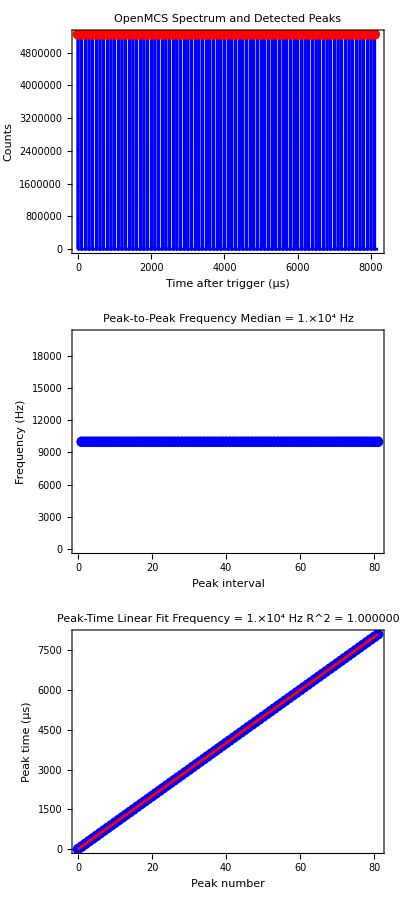

```mathematica
ClearAll["Global`*"];

(* ============================================================*)
(*USER SETTINGS*)
(* ============================================================*)

file=SystemDialogInput["FileOpen","Download"];

(*OpenMCS CSV columns*)
timeColumn=1;
countsColumn=2;

(*Unit used by the exported time column*)
timeUnit="ns";   (*"s","ms","us",or "ns"*)

(*Peak-detection settings*)
smoothingBins=1;
minimumPeakSeparationBins=5;
thresholdFraction=0.;


(* ============================================================*)
(*IMPORT DATA*)
(* ============================================================*)

If[file===$Canceled,Print["File selection cancelled."];
Abort[];];

rawData=Import[file,"Data"];

Print["Imported file: ",file];

data=Select[rawData,Length[#]>=Max[timeColumn,countsColumn]&&NumberQ[#[[timeColumn]]]&&NumberQ[#[[countsColumn]]]&];

If[Length[data]<3,Print["ERROR: Insufficient numeric data. Check the selected columns."];
Abort[];];


(* ============================================================*)
(*EXTRACT TIME AND COUNTS*)
(* ============================================================*)

timeRaw=N[data[[All,timeColumn]]];
counts=N[data[[All,countsColumn]]];


(*Convert imported time to seconds*)

timeScale=Switch[timeUnit,"s",1.,"ms",10^-3,"us",10^-6,"ns",10^-9,_,Print["ERROR: timeUnit must be s, ms, us, or ns."];
Abort[];];

timeSeconds=timeRaw*timeScale;


(* ============================================================*)
(*SORT DATA BY TIME*)
(* ============================================================*)

sortedData=SortBy[Transpose[{timeSeconds,counts}],First];

timeSeconds=sortedData[[All,1]];
counts=sortedData[[All,2]];


(* ============================================================*)
(*CALCULATE DWELL FROM TIME COLUMN*)
(* ============================================================*)

timeDifferences=Differences[timeSeconds];

validDifferences=Select[timeDifferences,#>0&];

If[Length[validDifferences]==0,Print["ERROR: Unable to calculate dwell time from time column."];
Abort[];];


(*Each consecutive row represents one MCS bin*)

timeBinSeconds=Median[validDifferences];

timeBinNanoseconds=timeBinSeconds*10^9;


Print[];
Print["================================================"];
Print["ACQUISITION INFORMATION"];
Print["================================================"];

Print["Number of data points: ",Length[counts]];

Print["Calculated dwell: ",ScientificForm[timeBinSeconds,8]," s/bin"];

Print["Calculated dwell: ",NumberForm[timeBinNanoseconds,{12,6}]," ns/bin"];

Print["Total time range: ",NumberForm[(Last[timeSeconds]-First[timeSeconds])*10^6,{12,6}]," us"];


(* ============================================================*)
(*SMOOTH DATA FOR PEAK DETECTION*)
(* ============================================================*)

smoothedCounts=GaussianFilter[counts,smoothingBins];

baseline=Median[smoothedCounts];

peakThreshold=baseline+thresholdFraction*(Max[smoothedCounts]-baseline);


(* ============================================================*)
(*FIND PEAKS*)
(* ============================================================*)

detectedPeaks=FindPeaks[smoothedCounts,1,minimumPeakSeparationBins,peakThreshold];

If[Length[detectedPeaks]<2,Print[];
Print["ERROR: Fewer than two peaks were detected."];
Print["Try reducing thresholdFraction or minimumPeakSeparationBins."];
Abort[];];

peakArrayPositions=detectedPeaks[[All,1]];


(* ============================================================*)
(*CONVERT ARRAY POSITIONS TO PHYSICAL TIME*)
(* ============================================================*)

positionToTime=Interpolation[Transpose[{Range[Length[timeSeconds]],timeSeconds}],InterpolationOrder->1];

positionToCounts=Interpolation[Transpose[{Range[Length[counts]],counts}],InterpolationOrder->1];


peakTimesSeconds=positionToTime/@peakArrayPositions;

peakCounts=positionToCounts/@peakArrayPositions;


(*Also express peak times in microseconds*)

peakTimesMicroseconds=peakTimesSeconds*10^6;


(* ============================================================*)
(*PEAK-TO-PEAK PERIOD CALCULATION*)
(* ============================================================*)

periodSeconds=Differences[peakTimesSeconds];

periodMicroseconds=periodSeconds*10^6;


(* ============================================================*)
(*INDIVIDUAL INTERVAL FREQUENCIES*)
(* ============================================================*)

intervalFrequenciesHz=1/periodSeconds;


(* ============================================================*)
(*MEDIAN PERIOD AND FREQUENCY*)
(* ============================================================*)

medianPeriodSeconds=Median[periodSeconds];

medianPeriodMicroseconds=medianPeriodSeconds*10^6;

medianFrequencyHz=1/medianPeriodSeconds;


(* ============================================================*)
(*MEAN PERIOD AND FREQUENCY*)
(* ============================================================*)

meanPeriodSeconds=Mean[periodSeconds];

meanPeriodMicroseconds=meanPeriodSeconds*10^6;

meanFrequencyHz=1/meanPeriodSeconds;


(* ============================================================*)
(*STANDARD DEVIATION OF PERIOD*)
(* ============================================================*)

periodStandardDeviation=StandardDeviation[periodSeconds];

periodStandardDeviationMicroseconds=periodStandardDeviation*10^6;


(* ============================================================*)
(*LINEAR-FIT FREQUENCY ESTIMATE*)
(* ============================================================*)

peakNumbers=Range[0,Length[peakTimesSeconds]-1];


peakTimeFit=LinearModelFit[Transpose[{peakNumbers,peakTimesSeconds}],n,n];


(*Slope of peak time versus peak number=period*)

fittedPeriodSeconds=Coefficient[Normal[peakTimeFit],n];

fittedPeriodMicroseconds=fittedPeriodSeconds*10^6;


(*Frequency from fitted period*)

fittedFrequencyHz=1/fittedPeriodSeconds;


(*Fit quality*)

rSquared=peakTimeFit["RSquared"];


(* ============================================================*)
(*PRINT FREQUENCY RESULTS*)
(* ============================================================*)

Print[];
Print["================================================"];
Print["PEAK / FREQUENCY ANALYSIS"];
Print["================================================"];

Print["Number of detected peaks: ",Length[peakTimesSeconds]];

Print[];

Print["Median period: ",ScientificForm[medianPeriodSeconds,8]," s"];

Print["Median period: ",NumberForm[medianPeriodMicroseconds,{12,6}]," us"];

Print["Median frequency: ",ScientificForm[medianFrequencyHz,10]," Hz"];

Print[];

Print["Mean period: ",ScientificForm[meanPeriodSeconds,8]," s"];

Print["Mean period: ",NumberForm[meanPeriodMicroseconds,{12,6}]," us"];

Print["Mean frequency: ",ScientificForm[meanFrequencyHz,10]," Hz"];

Print[];

Print["Period standard deviation: ",ScientificForm[periodStandardDeviation,8]," s"];

Print["Period standard deviation: ",NumberForm[periodStandardDeviationMicroseconds,{12,6}]," us"];

Print[];

Print["Linear-fit period: ",ScientificForm[fittedPeriodSeconds,10]," s"];

Print["Linear-fit period: ",NumberForm[fittedPeriodMicroseconds,{12,6}]," us"];

Print["Linear-fit frequency: ",ScientificForm[fittedFrequencyHz,10]," Hz"];

Print["Linear-fit R-squared: ",N[rSquared,10]];


(* ============================================================*)
(*RESULTS TABLE*)
(* ============================================================*)

resultTable=Table[{i,peakTimesSeconds[[i]],peakTimesMicroseconds[[i]],peakCounts[[i]],If[i==1,Missing["NotAvailable"],periodSeconds[[i-1]]],If[i==1,Missing["NotAvailable"],periodMicroseconds[[i-1]]],If[i==1,Missing["NotAvailable"],intervalFrequenciesHz[[i-1]]]},{i,Length[peakTimesSeconds]}];


resultDataset=Dataset[AssociationThread[{"Peak","Time (s)","Time (us)","Counts","Period (s)","Period (us)","Frequency (Hz)"},#]&/@resultTable];


(* ============================================================*)
(*FREQUENCY DATA*)
(* ============================================================*)

frequencyData=Transpose[{Range[Length[intervalFrequenciesHz]],intervalFrequenciesHz}];


(* ============================================================*)
(*SPECTRUM PLOT*)
(* ============================================================*)

spectrumPlot=Show[ListLinePlot[Transpose[{timeSeconds*10^6,counts}],PlotStyle->Blue,Frame->True,FrameLabel->{"Time after trigger (µs)","Counts"},PlotLabel->"OpenMCS Spectrum and Detected Peaks",PlotRange->All,ImageSize->Large],ListPlot[Transpose[{peakTimesSeconds*10^6,peakCounts}],PlotStyle->Directive[Red,PointSize[0.018]],PlotMarkers->Automatic]];


(* ============================================================*)
(*INTERVAL FREQUENCY PLOT*)
(* ============================================================*)

frequencyPlot=ListPlot[frequencyData,PlotStyle->Directive[Blue,PointSize[0.015]],PlotMarkers->Automatic,Frame->True,FrameLabel->{"Peak interval","Frequency (Hz)"},PlotLabel->Row[{"Peak-to-Peak Frequency   Median = ",ScientificForm[medianFrequencyHz,6]," Hz"}],PlotRange->All,ImageSize->Large];


(* ============================================================*)
(*LINEAR FIT PLOT*)
(* ============================================================*)

fitPlot=Show[ListPlot[Transpose[{peakNumbers,peakTimesSeconds*10^6}],PlotStyle->Directive[Blue,PointSize[0.018]],PlotMarkers->Automatic],Plot[peakTimeFit[n]*10^6,{n,First[peakNumbers],Last[peakNumbers]},PlotStyle->Red],Frame->True,FrameLabel->{"Peak number","Peak time (µs)"},PlotLabel->Row[{"Peak-Time Linear Fit   Frequency = ",ScientificForm[fittedFrequencyHz,8]," Hz   R^2 = ",NumberForm[rSquared,{8,6}]}],ImageSize->Large];


(* ============================================================*)
(*DISPLAY RESULTS*)
(* ============================================================*)

Print[];
Print["================================================"];
Print["DETECTED PEAK TABLE"];
Print["================================================"];
Print[];

Print[resultDataset];

Print[];

Column[{spectrumPlot,frequencyPlot,fitPlot}]
```